```mathematica
netdata1 = Import[StringJoin[NotebookDirectory[],"Neural Network Training Data/","trainedimageidentifyNetv2.wdx"]];
```

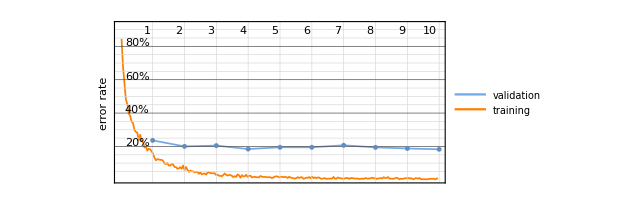

```mathematica
netdata1["ErrorRateEvolutionPlot"]
```

```mathematica
net1 = Import[StringJoin[NotebookDirectory[],"Neural Networks/","trainedimageidentifyNetv2.wlnet"]]
```

NetChain[<>]

```mathematica
netdata2 = Import[StringJoin[NotebookDirectory[],"Neural Network Training Data/","trainedinceptionNetv2.wdx"]];
```

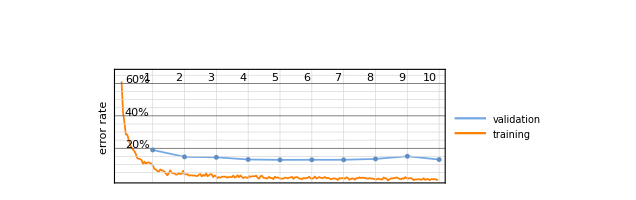

```mathematica
netdata2["ErrorRateEvolutionPlot"]
```

```mathematica
net2 = Import[StringJoin[NotebookDirectory[],"Neural Networks/","trainedinceptionNetv2.wlnet"]]
```

NetChain[<>]

```mathematica
netdata3 = Import[StringJoin[NotebookDirectory[],"Neural Network Training Data/","trainedademNetv2.mx"]];
```

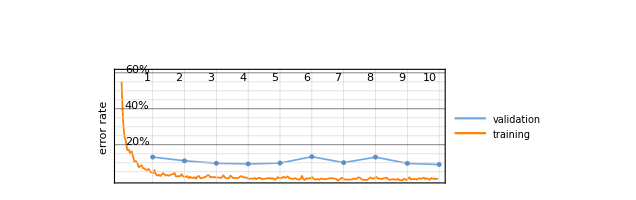

```mathematica
netdata3["ErrorRateEvolutionPlot"]
```

```mathematica
net3 =  Import[StringJoin[NotebookDirectory[],"Neural Networks/","trainedademNetv2.wlnet"]]
```

NetChain[<>]

```mathematica
netdata4 = Import[StringJoin[NotebookDirectory[],"Neural Network Training Data/","trainedresNetv2.mx"]];
```

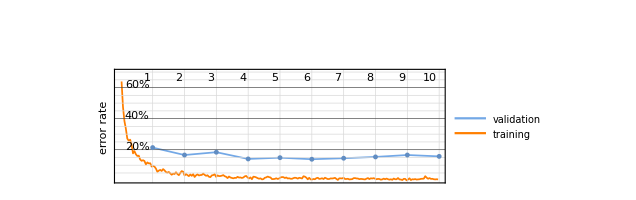

```mathematica
netdata4["ErrorRateEvolutionPlot"]
```

```mathematica
net4 = Import[StringJoin[NotebookDirectory[],"Neural Networks/","trainedresNetv2.wlnet"]]
```

NetChain[<>]

```mathematica
netdata5 = Import[StringJoin[NotebookDirectory[],"Neural Network Training Data/","trainedvgg19Netv2.mx"]];
```

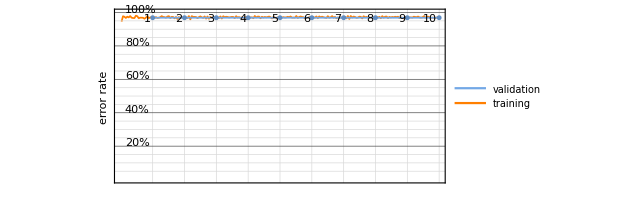

```mathematica
netdata5["ErrorRateEvolutionPlot"]
```

```mathematica
net5 = Import[StringJoin[NotebookDirectory[],"Neural Networks/","trainedvgg19Netv2.wlnet"]]
```

NetChain[<>]

```mathematica
netdata6 = Import[StringJoin[NotebookDirectory[],"Neural Network Training Data/","trainedimageidentifyNet.mx"]];
```

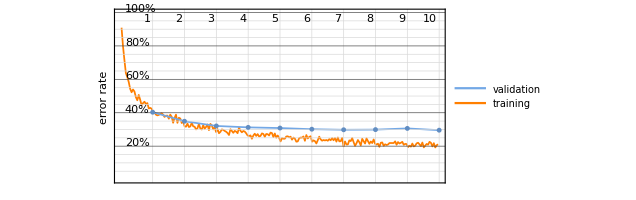

```mathematica
netdata6["ErrorRateEvolutionPlot"]
```

```mathematica
net6 = Import[StringJoin[NotebookDirectory[],"Neural Networks/","trainedimageidentifyNet.wlnet"]]
```

NetChain[<>]

```mathematica
netdata7 = Import[StringJoin[NotebookDirectory[],"Neural Network Training Data/","trainedademNet.mx"]];
```

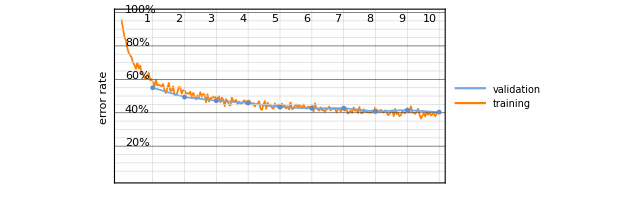

```mathematica
netdata7["ErrorRateEvolutionPlot"]
```

```mathematica
net7 = Import[StringJoin[NotebookDirectory[],"Neural Networks/","trainedademNet.wlnet"]]
```

NetChain[<>]

```mathematica
netdata8 = Import[StringJoin[NotebookDirectory[],"Neural Network Training Data/","trainedresNet.mx"]];
```

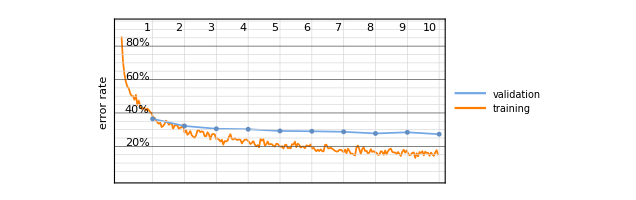

```mathematica
netdata8["ErrorRateEvolutionPlot"]
```

```mathematica
net8 = Import[StringJoin[NotebookDirectory[],"Neural Networks/","trainedresNet.wlnet"]]
```

NetChain[<>]

```mathematica
netdata9 = Import[StringJoin[NotebookDirectory[],"Neural Network Training Data/","trainedinceptionNet.mx"]];
```

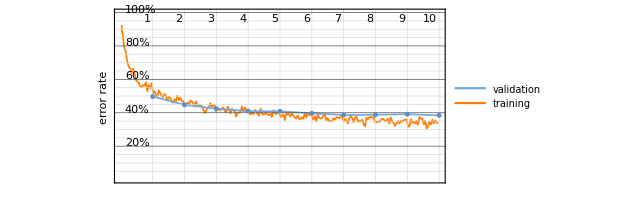

```mathematica
netdata9["ErrorRateEvolutionPlot"]
```

```mathematica
net9 = Import[StringJoin[NotebookDirectory[],"Neural Networks/","trainedinceptionNet.wlnet"]]
```

NetChain[<>]

```mathematica
netdata10 = Import[StringJoin[NotebookDirectory[],"Neural Network Training Data/","trainedvgg19Net.mx"]];
```

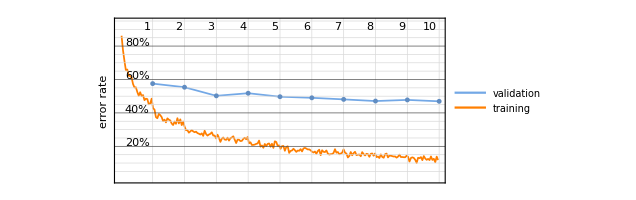

```mathematica
netdata10["ErrorRateEvolutionPlot"]
```

```mathematica
net10 = Import[StringJoin[NotebookDirectory[],"Neural Networks/","trainedvgg19Net.wlnet"]]
```

NetChain[<>]

```mathematica
URLShorten@CloudExport[net3,"MX",Permissions->"Public"]
```

```mathematica
URLShorten@CloudExport[net2,"MX",Permissions->"Public"]
```

```mathematica
URLShorten@CloudExport[net4,"MX",Permissions->"Public"]
```

```mathematica
URLShorten@CloudExport[net1,"MX",Permissions->"Public"]
```

```mathematica
URLShorten@CloudExport[net8,"MX",Permissions->"Public"]
```

```mathematica
URLShorten@CloudExport[net6,"MX",Permissions->"Public"]
```

```mathematica
URLShorten@CloudExport[net9,"MX",Permissions->"Public"]
```

```mathematica
URLShorten@CloudExport[net7,"MX",Permissions->"Public"]
```

```mathematica
URLShorten@CloudExport[net10,"MX",Permissions->"Public"]
```

```mathematica
URLShorten@CloudExport[ net5,"MX",Permissions->"Public"]
```

```mathematica
nets = {"https://wolfr.am/w1c1UK2b","https://wolfr.am/w1cdYBTo","https://wolfr.am/w1ce015I","https://wolfr.am/w1ce1kfz","https://wolfr.am/w1cfx64j","https://wolfr.am/w1cfNQlX","https://wolfr.am/w1cgpcDC","https://wolfr.am/w1cjsozw","https://wolfr.am/w1ck33t9","https://wolfr.am/w1ckD0rh"};
```

```mathematica
form=FormPage[{"Upload"->"Image","Network"->{"Ademxapp v2"->1,"Inception V3 v2"->2,"ResNet-152 v2"->3,"ImageIdentify v2"->4,"ResNet-152 v1"->5,"ImageIdentify v1"->6,"Inception v1"->7,"Ademxapp v1"->8,"VGG-19 v1"->9,"VGG-19 v2"->10}},(
nets= {"https://wolfr.am/w1c1UK2b","https://wolfr.am/w1cdYBTo","https://wolfr.am/w1ce015I","https://wolfr.am/w1ce1kfz","https://wolfr.am/w1cfx64j","https://wolfr.am/w1cfNQlX","https://wolfr.am/w1cgpcDC","https://wolfr.am/w1cjsozw","https://wolfr.am/w1ck33t9","https://wolfr.am/w1ckD0rh"};
network = CloudImport[nets[[#Network]]];
result=network[#Upload];
Style[result,"Title"])&,
AppearanceRules-><|"Title"->"Identify Plugs and Connectors","Description"->"This is an implementation of various Neural Networks which can identify Plugs and Connectors"|>]

CloudDeploy[form,"PlugID",Permissions->"Public"]
```

```mathematica
URLShorten@CloudObject[["https://www.wolframcloud.com/objects/rishab/PlugID"](https://www.wolframcloud.com/objects/rishab/PlugID)]
```

https://wolfr.am/w14jKMnl

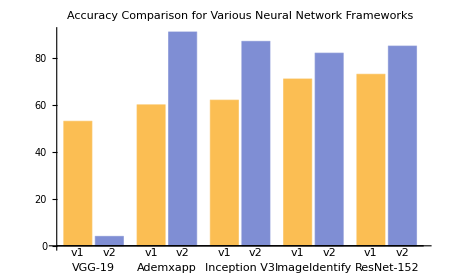

```mathematica
BarChart[{Labeled[{53,4},"VGG-19"],Labeled[{60,91},"Ademxapp"],Labeled[{62,87},"Inception V3"],Labeled[{71,82},"ImageIdentify"],Labeled[{73,85},"ResNet-152"]},ChartLabels->{"v1","v2"},PerformanceGoal->"Quality",PlotLabel->"Accuracy Comparison for Various Neural Network Frameworks"]
```

```mathematica
ListLinePlot[{Callout[0.25,"VGG-19 v1"],Callout[0.256,"VGG-19 v2"],Callout[1.20,"Ademxapp v1"],Callout[1.10,"Ademxapp v2"],Callout[0.15,"Inception V3 v1"],Callout[0.14,"Inception V3 v2"],Callout[0.069,"ImageIdentify v1"],Callout[0.062,"ImageIdentify v2"],Callout[0.18,"ResNet-152 v1"],Callout[0.14,"ResNet-152 v2"]},Ticks->{False,True},PlotLabel->"Speed Comparison for Various Neural Network Frameworks"]
```

-Graphics-